## images

```mathematica
CurrentImage[]
```

CurrentImage::checkcam: The camera 4M HD Camera is not available. Check that the camera is properly connected and that it is not currently in use by another application.

$Failed

```mathematica
Import@"https://ts1.cn.mm.bing.net/th/id/R-C.4df22bab119d2a4c455ba711fe1e896b?rik=MgK0u8FMZmeZOA&riu=http%3a%2f%2ffencing4horses.com.au%2fwp-content%2fuploads%2f2018%2f09%2fCrimping-Tool-350.jpg&ehk=%2b6ONZOEsfIOwOTgaP01Pl7xoiXywQ5atsX5tYctYUAE%3d&risl=&pid=ImgRaw&r=0"
```

```mathematica
ImageResize[-Graphics-,120]
```

-Graphics-

```mathematica
ColorNegate@-Graphics-
```

-Graphics-

```mathematica
Blur@-Graphics-
```

-Graphics-

```mathematica
FaceRecognize[]
```

```mathematica
Table[Blur[-Graphics-,n],{n,0,15,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DominantColors[-Graphics-]
```

{RGBColor[0.2785262937606573, 0.34612449471554374, 0.5214066511492738],RGBColor[0.10248209904760239, 0.16880294998427195, 0.3628396414283156],RGBColor[0.7426844056120736, 0.7383989575178522, 0.7914659834796278],RGBColor[0.37689999674971314, 0.7999946001805079, 0.8402431567603407],RGBColor[0.08898189094679662, 0.09296387025419747, 0.1164052693644691]}

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
Manipulate[Binarize[-Graphics-,n],{{n,.5},0,1}]
```

```mathematica
Manipulate[
Graphics[Disk[{0,0},n],PlotRange->1],
{{n,.5},0,1}
]
```

```mathematica
Manipulate[Plot[Sin[ax+b],{x,0,6}],{a,1,4},{b,0,10}]
```

```mathematica
Manipulate[EdgeDetect[-Graphics-,r],{{r,1},1,15}]
```

```mathematica
a=ImageData[ImageResize[-Graphics-,640]];
```

```mathematica
part=a[[20;;250,1;;300]];
Image@part
```

-Graphics-

```mathematica
RGBColor@a[[21,10]]
```

RGBColor[{0.996078431372549, 0.996078431372549, 0.996078431372549, 1.}]

```mathematica
Position[a,0];
```

```mathematica
anim = {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-};
```

```mathematica
image3D=Image3D[anim,ColorFunction->"GrayLevelOpacity",BoxRatios->{1,1,1/4}]
```

-Graphics3D-

```mathematica
Image3DSlices[Blur[image3D,{3,0,0}],{10}][[1]]
```

-Graphics-

## Strings & Texts

```mathematica
StringLength["hello"]
```

5

```mathematica
ToUpperCase["I'm coding in the Wolfram Language!哈哈"]
```

I'M CODING IN THE WOLFRAM LANGUAGE!哈哈

```mathematica
StringJoin["Hello", " ", "there!", " How are you?"]
```

Hello there! How are you?

```mathematica
StringTake[{"you","me","hey"},3]
```

StringTake::take: Cannot take positions 1 through 3 in "me".

{you,StringTake[me,3],hey}

```mathematica
Characters["a string is made of characters"]
```

{a, ,s,t,r,i,n,g, ,i,s, ,m,a,d,e, ,o,f, ,c,h,a,r,a,c,t,e,r,s}

```mathematica
Sort[Characters["a string of characters"]]
```

{ , , ,a,a,a,c,c,e,f,g,h,i,n,o,r,r,r,s,s,t,t}

```mathematica
InputForm@TextWords["This is a sentence. Sentences are made of words."]
```

{"This", "is", "a", "sentence", "Sentences", "are", "made", "of", "words"}

```mathematica
Characters["10月6号继续上课，因为学校只放3天。东南大学真有你的"]
```

{1,0,月,6,号,继,续,上,课,，,因,为,学,校,只,放,3,天,。,东,南,大,学,真,有,你,的}

```mathematica
TextWords["10月6号继续上课，因为学校只放3天。东南大学真有你的"]
```

{10月6号继续上课,因为学校只放3天,东南大学真有你的}

```mathematica
TextWords["10月 6号 继续 上课，因为 学校 只 放 3天。东南大学 真有你的"]
```

{10月,6号,继续,上课,因为,学校,只,放,3天,东南大学,真有你的}

```mathematica
data=EntityValue[CountryData[],{"Name","Population"}];
```

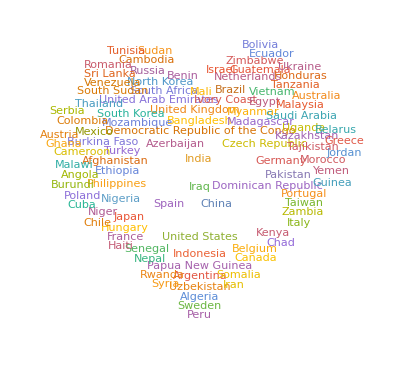

```mathematica
WordCloud[data, -Graphics-]
```

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Range[4,12,2]
```

{4,6,8,10,12}

```mathematica
CharacterRange["a","t"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t}

```mathematica
Alphabet["German"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
a=TextTranslation["您吃饭了吗","German"]
```

Hast du gegessen?

```mathematica
b=TextTranslation["Good morning","Chinese"]
```

早上好

```mathematica
ToCharacterCode["A","UTF8"]
```

{65}

```mathematica
BaseForm[65,16]
```

41_16

```mathematica
ToCharacterCode["好","UTF8"]
```

{229,165,189}

```mathematica
Style["可以",60]
```

可以

```mathematica
Rasterize@Style["可以",60]
```

-Graphics-

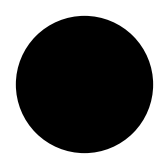

```mathematica
g=Graphics[Disk[{0,0},1]]
```

```mathematica
Rasterize[g,RasterSize->50]
```

-Graphics-

## Sound

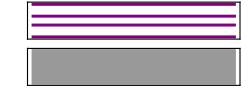

```mathematica
Sound[SoundNote[{"C","E","G","B"}]]
```

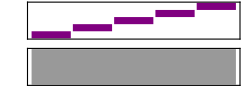

```mathematica
Sound[Table[SoundNote[n,0.1],{n,5}]]
```

```mathematica
Speak["test"]
```

```mathematica
audio = Audio[File["ExampleData/car.mp3"]]
```

```mathematica
AudioData@audio
```

{{0.,1.79305×10^-12,-8.86338×10^-13,5.4782×10^-14,-1.70149×10^-13,-4.65504×10^-13,3.774×10^-13,-4.8931×10^-13,-4.41624×10^-13,1.39072×10^-12,328300,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}
 |  |  |  |

```mathematica
ListLinePlot@AudioData@audio
```

-Graphics-

```mathematica
Audio@AudioData[audio][[1,1;;100000]]
```

## Assigning Names to Things

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
%
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
%+1
```

{2,3,4,5,6,7,8,9,10,11}

```mathematica
param=1
Information@param
```

1

Information[1]

```mathematica
Module[
{x=Range[10],n=2},
x+n
]
```

{3,4,5,6,7,8,9,10,11,12}

```mathematica
Module[
{x,n=2,res1,res2},
x=Range[10];
res1 = x^n;
res2=x+55;
{res1,res2}
]
```

{{1,4,9,16,25,36,49,64,81,100},{56,57,58,59,60,61,62,63,64,65}}

## Immediate and Delayed Values

```mathematica
n=12
```

12

```mathematica
circles:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
```

```mathematica
Circles[n_]:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
```

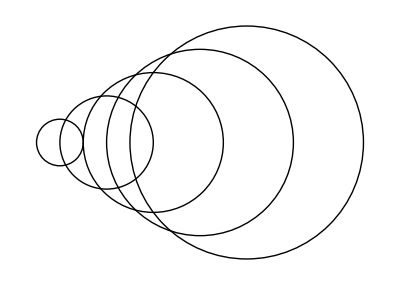

```mathematica
Circles[5]
```

```mathematica
MyAdd[x_]:=x+1
```

```mathematica
Information@MyAdd
```

```mathematica
MyAdd[66]
```

67